# 4. Time-Varying Intensity and Frequency Noise

## Parameters:

```mathematica
ClearAll[Δν,f,fmin, fmax, df,t,Ω,Ω0,timeupperbound,Nrun]

Nrun=50;(* Number of runs in averaging *)

νmin=0.000;


Ω0=(10 10^6)×2π ;(* Rabi oscillation frequency *)
ntime=1;
Δν0=νmin; (* Laser linewidth, νFWHM of a Lorentzian lineshape *)
timeupperbound=0.5( ntime+1)*2π/Ω0;(* Time range for simulation *)

fmin=100*40; (* Sampling width and start/end frequency *)
fmax=200000*40;

df=fmin;

RINlevelmin=0.000;
RINlevelmax=0.1;
dRINlevel=0.005;
Nsweep=(RINlevelmax-RINlevelmin)/dRINlevel;

RINbw=fmax;

Srin[f_,RIN_]:=If[f<RINbw,RIN^2/(2*RINbw),0];
Sϕ[f_,Δν_]:=(Δν*Ω0)^2/(2fmax* f^2);(* Calculating phase noise PSD with frequency noise PSD *)
```

## Averaging on Multiple Runs:

Nrun= 50

RIN=0.005  Pr=0.999988 at time 1π/Ω

RIN=0.01  Pr=0.999953 at time 1π/Ω

RIN=0.015  Pr=0.999878 at time 1π/Ω

RIN=0.02  Pr=0.999824 at time 1π/Ω

RIN=0.025  Pr=0.999557 at time 1π/Ω

RIN=0.03  Pr=0.999593 at time 1π/Ω

RIN=0.035  Pr=0.999331 at time 1π/Ω

RIN=0.04  Pr=0.999181 at time 1π/Ω

RIN=0.045  Pr=0.998812 at time 1π/Ω

RIN=0.05  Pr=0.999245 at time 1π/Ω

RIN=0.055  Pr=0.998708 at time 1π/Ω

RIN=0.06  Pr=0.998329 at time 1π/Ω

RIN=0.065  Pr=0.996993 at time 1π/Ω

RIN=0.07  Pr=0.996586 at time 1π/Ω

RIN=0.075  Pr=0.996408 at time 1π/Ω

RIN=0.08  Pr=0.997013 at time 1π/Ω

RIN=0.085  Pr=0.995658 at time 1π/Ω

RIN=0.09  Pr=0.995694 at time 1π/Ω

RIN=0.095  Pr=0.994279 at time 1π/Ω

RIN=0.1  Pr=0.994351 at time 1π/Ω

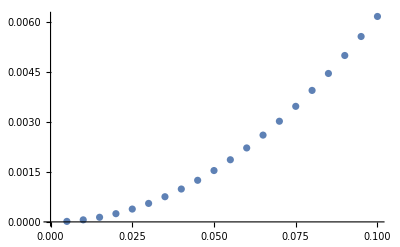

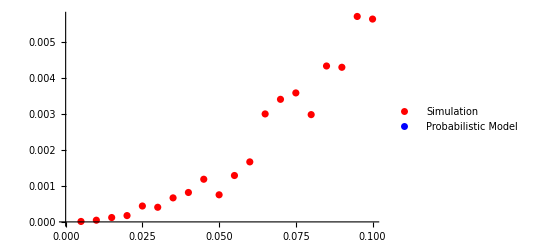

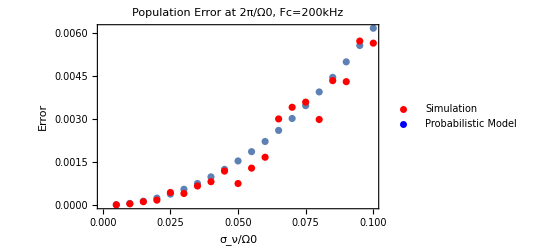

```mathematica
ClearAll[a,b,t,i,j,prj,SumPrj, Pr];
Print["Nrun= ",Nrun]
Pr=Table[0,Nsweep];
Perror=Table[0,Nsweep];
Rin=0;
Do[
Rin=RINlevelmin+j dRINlevel;
Do[
(*ϕcarrier=Sum[2√Sϕ[f,Δν]Cos[2π f t +RandomReal[{0,2π} ]]√df,{f,fmin,fmax,df}]; (* Phase noise time series generation with its PSD *)
ϕ=ϕcarrier; 
*)
ϕ=0;
Rcarrier=Sum[2√Srin[f,Rin]Cos[2π f t +RandomReal[{0,2π} ]]√df,{f,fmin,fmax,df}];
Ω=Ω0*Sqrt[1+Rcarrier];

sol=NDSolve[{a'[t]==I (Ω/2) Exp[I ϕ]b[t],b'[t]==I (Ω/2) Exp[-I ϕ]a[t],a[0]==1, b[0]==0},{a,b},{t,0,timeupperbound}];(* Solving Rabi oscillation equations*)

bm[i]=Evaluate[b[t]/.sol];,
{i,1,Nrun}];
Prj=Table[Abs[Evaluate[bm[i]//.t->Range[0,timeupperbound,π/Ω0]]^2][[1]],{i,1,Nrun}];
SumPrj=Total[Prj[[All,ntime+1]]];
Print[" RIN=",N[Rin],"  Pr=",SumPrj/Nrun," at time "<>ToString[ntime]<>"π/Ω"];
Pr[[j]]=1-SumPrj/Nrun;
Perror[[j]]=StandardDeviation[Prj[[All,ntime+1]]],

{j,1,Nsweep}];
NN=IntegerPart[Nsweep];
dsigma=dRINlevel;

ym=Array[0,NN];
xm=Array[0,NN];
Do[
ym[[i]]=(1*π^2(i*dsigma)^2)/(4*4);
xm[[i]]=dsigma*i;
,{i,1,NN}];

data1=Transpose@{xm,ym};
p1=ListPlot[data1]
data2=Transpose@{xm,Pr};
p2=ListPlot[data2,PlotStyle->Red,PlotLegends->LineLegend[{Red,Blue},{"Simulation","Probabilistic Model"}]]
Show[{p1,p2},Frame->True,FrameLabel->{"σ_ν/Ω0","Error"},PlotLabel->"Population Error at 2π/Ω0, Fc=200kHz"]
```

-Graphics-

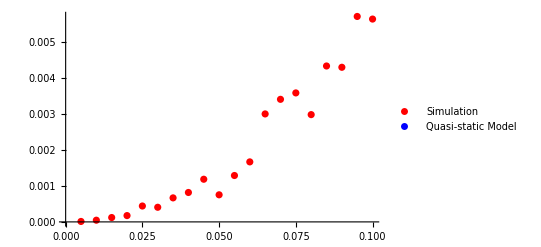

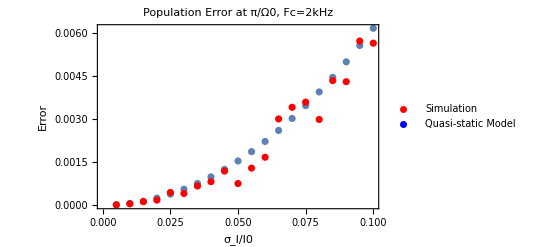

```mathematica
dsigma=dRINlevel;

ym=Array[0,NN];
xm=Array[0,NN];
Do[
ym[[i]]=(1*π^2(i*dsigma)^2)/(4*4);
xm[[i]]=dsigma*i;
,{i,1,NN}];

data1=Transpose@{xm,ym};
p1=ListPlot[data1]
data2=Transpose@{xm,Pr};
p2=ListPlot[data2,PlotStyle->Red,PlotLegends->LineLegend[{Red,Blue},{"Simulation","Quasi-static Model"}]]
Show[{p1,p2},Frame->True,FrameLabel->{"σ_I/I0","Error"},PlotLabel->"Population Error at π/Ω0, Fc=2kHz"]
```

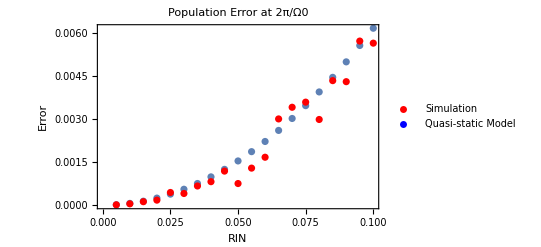

```mathematica
Show[{p1,p2},Frame->True,FrameLabel->{Style["RIN",Bold,16],Style["Error",Bold,16]},PlotLabel->Style["Population Error at 2π/Ω0",Bold,16]]
```